## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/mercury/MoM-plots/";  
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/mercury/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.138071 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Apr 20, 2020, time: 17:06:29

nb: /Users/dantopa/Mathematica_files/nb/ert/mercury/MoM-plots/meanRCS-monomial-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.138071 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,3},{Automatic,Automatic}};
```

```mathematica
isize=ImageSize->5 72;
```

```mathematica
θticks={{1,"-180°"},{91,"-90°"},{181,"0°"},{271,"90°"},{361,"180°"}};
```

```mathematica
fticks={{Automatic,Automatic},{θticks,Automatic}};
```

#### functions

#### substitutions

#### modules

## master color scheme

### import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
σ=meanRCS[[1]];
{M,𝒩}=Dimensions[meanRCS]
```

{28,361}

```mathematica
S=meanRCSᵀ;
```

```mathematica
mx=Max[meanRCS]
mn=Min[meanRCS]
```

59.2522

0.798997

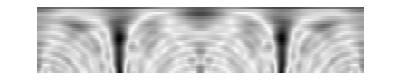

ArrayPlot::mat: Argument σ at position 1 is not a list of lists.

ArrayPlot[σ]

```mathematica
ArrayPlot[meanRCS]
```

```mathematica
ListPlot[{Range[3,30],S[[1]]}ᵀ,
PlotRange->{{2,31},Automatic},
PlotStyle->Blue,
PlotLabel->"Yaw angle α = "<>ToString[k-1],
Frame->True,
FrameLabel->{"Radar Frequency, MHz","Mean Total Cross Section, sq m"},
ipad]
```

## sequence

```mathematica
Do[
α=k-1;
g=ListPlot[{Range[3,30],S[[k]]}ᵀ,
PlotRange->{{2,31},Automatic},
PlotStyle->Blue,
PlotLabel->"Yaw angle α = "<>ToString[-180+k-1],
Frame->True,
FrameLabel->{"Radar Frequency, MHz","Mean Total Cross Section, sq m"},
ipad];
Export[dirGraph<>"monomial-"<>pad[k,3]<>".gif",g]
,{k,181}]
```

## slices

### data

```mathematica
colA=σᵀ[[90]]
```

{56.4461,58.2176,56.8392,53.2168,49.5602,47.5605,47.5739,48.5629,48.79,48.601,49.44,51.1751,51.5718,50.9318,49.4575,50.6049,42.9274,29.9927,27.1447,27.3608,31.314,36.2898,39.4069,38.8113,41.6111,44.7139,48.5529,52.9072}

```mathematica
colB=σᵀ[[180]]
```

{10.8892,7.58241,12.9625,21.1692,21.0069,19.0777,25.6229,25.1543,17.3429,15.4267,13.941,11.1631,18.603,27.3713,26.9742,28.0041,39.3875,38.153,42.7898,42.2806,32.6415,27.611,23.6047,22.8299,22.97,17.2574,7.64881,7.19914}

```mathematica
colC=σᵀ[[135]]
```

{16.3436,14.9248,12.8702,8.27467,6.45184,7.05194,8.68654,7.71545,6.58663,6.82613,10.6063,11.9927,11.0696,12.062,14.208,15.591,27.8959,11.9479,1.98442,9.5965,13.9928,15.0537,16.164,18.3667,17.2392,15.8062,16.6624,15.6643}

### plots

```mathematica
gA=ListPlot[{Range[3,30],colA}ᵀ,Frame->True,PlotStyle->Black]
```

Transpose::nmtx: The first two levels of {{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30},colA} cannot be transposed.

Transpose::nmtx: The first two levels of {{3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,«4»,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.},colA} cannot be transposed.

Transpose::nmtx: The first two levels of {{3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.},colA} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.},colA}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Transpose[{{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30},colA}],Frame→True,PlotStyle→GrayLevel[0]]

```mathematica
gB=ListPlot[colB,Frame->True,PlotStyle->Black]
gC=ListPlot[colC,Frame->True,PlotStyle->Black]
```

## fits

```mathematica
data=colA;
x=Range[M];
one=Table[1,{M}];
d=7;
basis=Table[𝓍^k,{k,0,d}];
A={one};
vec=one;
Do[
vec=x vec;
A=AppendTo[A,vec]
,{k,d}];
A=Aᵀ;
```

```mathematica
A//mf;
```

```mathematica
c=LeastSquares[A,data]
```

{37.4275,27.8436,-11.7317,2.00626,-0.169241,0.00743199,-0.000163001,1.4124×10^-6}

```mathematica
Clear[f];
f[𝓍_]=c.basis
```

37.4275+27.8436 𝓍-11.7317 𝓍^2+2.00626 𝓍^3-0.169241 𝓍^4+0.00743199 𝓍^5-0.000163001 𝓍^6+1.4124×10^-6 𝓍^7

```mathematica
r=A.c-data
```

{-1.06243,1.5402,0.684839,-0.0806838,-0.410925,-0.813743,-1.39725,-1.45523,0.120026,2.26769,2.89607,1.65713,0.525797,-0.823776,-2.40094,-7.29312,-3.57029,5.7279,5.75576,3.93414,-0.171653,-3.81058,-4.28298,-0.119839,1.03727,1.69985,0.960324,-1.11279}

```mathematica
r.r
```

218.273

```mathematica
𝓈=√((r.r)/(M-(d+1))Diagonal[Inverse[A†.A]])
```

{9.76428,10.6691,3.89098,0.657519,0.0582788,0.00279423,0.0000685427,6.73789×10^-7}

```mathematica
sn=c/𝓈
```

{3.8331,2.60974,-3.0151,3.05127,-2.904,2.65976,-2.37809,2.0962}

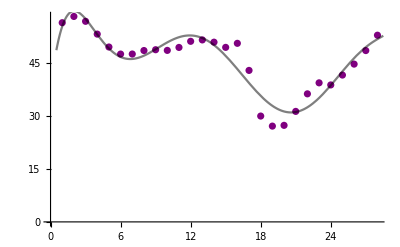

```mathematica
gplot=ListPlot[data,PlotStyle->Purple];
gp=Plot[f[z],{z,1/2,M+1/2},PlotStyle->{Black,Opacity[0.5]}];
Show[{gplot,gp}]
```

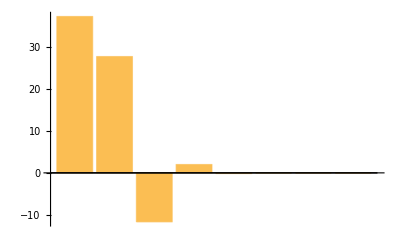

```mathematica
BarChart[c]
```

## fits

```mathematica
data=colB;
x=Range[M];
one=Table[1,{M}];
d=7;
basis=Table[𝓍^k,{k,0,d}];
A={one};
vec=one;
Do[
vec=x vec;
A=AppendTo[A,vec]
,{k,d}];
A=Aᵀ;
```

```mathematica
A//mf;
```

```mathematica
c=LeastSquares[A,data]
```

{31.6443,-34.3301,16.4882,-3.15289,0.294823,-0.0143006,0.000345972,-3.3052×10^-6}

```mathematica
Clear[f];
f[𝓍_]=c.basis
```

31.6443-34.3301 𝓍+16.4882 𝓍^2-3.15289 𝓍^3+0.294823 𝓍^4-0.0143006 𝓍^5+0.000345972 𝓍^6-3.3052×10^-6 𝓍^7

```mathematica
r=A.c-data
```

{0.0411403,0.412799,-0.391628,-2.62425,1.80495,5.24522,-2.30353,-4.42373,0.378992,-0.0515709,0.543001,4.28675,-0.343867,-4.84426,0.616044,4.62821,-2.56259,1.31506,-2.6764,-3.62746,2.71609,3.23604,2.37271,-1.20326,-4.60647,-1.27551,5.23583,-1.89898}

```mathematica
r.r
```

234.471

```mathematica
𝓈=√((r.r)/(M-(d+1))Diagonal[Inverse[A†.A]])
```

{10.1201,11.0579,4.03277,0.68148,0.0604026,0.00289606,0.0000710405,6.98343×10^-7}

```mathematica
sn=c/𝓈
```

{3.12687,-3.10458,4.08857,-4.62653,4.88097,-4.93795,4.87006,-4.73291}

```mathematica
gplot=ListPlot[data,PlotStyle->Purple];
gp=Plot[f[z],{z,1/2,M+1/2},PlotStyle->{Black,Opacity[0.5]}];
Show[{gplot,gp}]
```

```mathematica
BarChart[c]
```

## plots

```mathematica
gdvf=Show[{gplot,gp},
ipad,
isize,
Frame->True,
FrameLabel->{"Radar Frequency, MHz","Mean Total RCS, sq m"},FrameTicks->{{Automatic,Automatic},{{{1,3},{8,10},{18,20},{28,30}},Automatic}},
PlotLabel->"MoM RCS vs Monomial Expansion"<>lf<>"Yaw angle = 0"]
```

```mathematica
z={Range[3,30],r}ᵀ;
gres=ListPlot[z,
ipad,
isize,
Frame->True,
FrameLabel->{"Radar Frequency, MHz","Mean Total RCS, sq m"},PlotStyle->Red,
PlotLabel->"Monomial Approximation Error"<>lf<>"Yaw angle = 0"]
```

```mathematica
gbars=BarChart[c,
Frame->True,
PlotLabel->"Amplitudes for d = "<>ToString[d]<>lf<>"Yaw angle = 0",
ChartStyle->{{Blue},{Opacity[0.1]}},
FrameTicks->{{Automatic,Automatic},{Table[
{k+1,Subscript["a",k]}
,{k,0,d}],Automatic}},
ipad,isize]
```

```mathematica
ebars=Table[
{k-1,Around[c[[k]],𝓈[[k]]]}
,{k,Length[c]}];
gebars=ListPlot[ebars,
isize,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Table[{k,Subscript["a",k]},{k,0,Length[ebars]}],Automatic}},
PlotLabel->"Amplitudes with errors for d = "<>ToString[d]<>lf<>"Yaw angle = 0",
PlotStyle->Blue,
PlotRange->{{-0.5,d+0.5},Full},
isize,ipad]
```

## table of values

```mathematica
Table[
index=k+1;
str="            $a_{"<>ToString[k]<>"}$ ";
str=str<>"& = & ";
(* amplitude *)
a=c[[index]];
ipart=IntegerPart[a];
fpart=FractionalPart[Abs[a]];
(* amp to string *)
str=str<>"$"<>ToString[ipart]<>"$";
num=ToString[Round[(1000 fpart)/10]];
str=str<>" & ";
str=str<>"$"<>num<>"$";
str=str<>" & $@pm$ & ";
(* error *)
a=𝓈[[index]];
ipart=IntegerPart[a];
fpart=FractionalPart[Abs[a]];
(* err to string *)
str=str<>"$"<>ToString[ipart]<>"$";
num=ToString[Round[(1000 fpart)/10]];
str=str<>" & ";
str=str<>"$"<>num<>"$ @@";
Print[str];
,{k,0,d}];
```

$a_{0}$ & = & $31$ & $64$ & $@pm$ & $10$ & $12$ @@

$a_{1}$ & = & $-34$ & $33$ & $@pm$ & $11$ & $6$ @@

$a_{2}$ & = & $16$ & $49$ & $@pm$ & $4$ & $3$ @@

$a_{3}$ & = & $-3$ & $15$ & $@pm$ & $0$ & $68$ @@

$a_{4}$ & = & $0$ & $29$ & $@pm$ & $0$ & $6$ @@

$a_{5}$ & = & $0$ & $1$ & $@pm$ & $0$ & $0$ @@

$a_{6}$ & = & $0$ & $0$ & $@pm$ & $0$ & $0$ @@

$a_{7}$ & = & $0$ & $0$ & $@pm$ & $0$ & $0$ @@

```mathematica
c
```

{31.6443,-34.3301,16.4882,-3.15289,0.294823,-0.0143006,0.000345972,-3.3052×10^-6}

```mathematica
𝓈
```

{10.1201,11.0579,4.03277,0.68148,0.0604026,0.00289606,0.0000710405,6.98343×10^-7}

## export

```mathematica
tresExport["monomial-fit-data",gdvf];
tresExport["monomial-residuals",gres];
tresExport["monomial-bar-chart",gbars];
tresExport["monomial-error-bars",gebars]
```

## plot

```mathematica
(* function *)
g001=Plot[f[z],{z,1/2,M+1/2},
PlotRange->Full,
Frame->True,
FrameTicks->fticks,
PlotStyle->{Opacity[0.25],Blue}]
```

```mathematica
(* bar chart *)
gbars=BarChart[c,
Frame->True,
PlotLabel->"Amplitudes for d = "<>ToString[d]<>lf<>subtitle,
ChartStyle->{{Blue},{Opacity[0.1]}},
FrameTicks->{{Automatic,Automatic},{Table[
{k+1,Subscript["a",k]}
,{k,0,d}],Automatic}},
ipad,isize];
(* amplitudes with errors *)
ebars=Table[
{k-1,Around[c[[k]],ϵ[[k]]]}
,{k,Length[c]}];
gebars=ListPlot[ebars,
isize,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Table[{k,Subscript["a",k]},{k,0,Length[ebars],2}],Automatic}},
PlotLabel->"Amplitudes with errors for d = "<>ToString[d]<>lf<>subtitle,
PlotStyle->Blue,
PlotRange->{{-0.5,d+0.5},Full},
isize,ipad];
(* compare data to fit *)
dsubtitle=subtitle<>", d = "<>ToString[d];
ga=Show[{g001,g000},
PlotLabel->sty["MoM RCS vs Fourier Cosine Expansion"<>lf<>dsubtitle],
FrameLabel->{sty["Yaw angle, α"],sty["Mean total RCS, <σ_T>, m^2"]},
FrameTicks->fticks,
Axes->{False,True},
PlotRange->{bot,top},
isize,ipad];
(* residual error *)
gb=ListPlot[R,
Frame->True,
FrameTicks->fticks,
FrameLabel->{sty["Yaw angle, α"],sty["Residual error, m^2"]},
(* PlotRange->Λ{-1,1}, *)
PlotStyle->{Red,PointSize[0.005]},
PlotLabel->sty["Fourier Approximation Error"<>lf<>dsubtitle],
isize,ipad];
(* group plots *)
gout2=GraphicsRow[{ga,gb},
PlotRange->{bot,top},
ImageSize->12 72];
gout4=GraphicsGrid[{{ga,gb},{gbars,gebars}},
ImageSize->12 72];(* output *)
(* tresExport["fit-rcs-cos-"<>pad[ν]<>"-"<>pad[d],ga]; *)
tresExport["data-fit-rcs-cos-"<>pad[ν]<>"-"<>pad[d],ga];
tresExport["residual-rcs-cos-"<>pad[ν]<>"-"<>pad[d],gb];
tresExport["amplitudes-rcs-cos-"<>pad[ν]<>"-"<>pad[d],gebars];
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```